```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
PlotPr[rTilde_]:=Show[Histogram[rTilde,Automatic,"PDF",PlotRange->{{0.,1.},{-0.01,2.01}},Frame->True,FrameStyle->Directive[Black,FontSize->20],FrameLabel->{HoldForm[r̃], HoldForm[P[r̃]]},ImageSize->400],Plot[27/4*(r+r^2)/((1+r+r^2)^(5/2)),{r,0,1},PlotStyle->Directive[Blue,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],
Plot[2/(1+r)^2,{r,0,1},PlotStyle->Directive[Red,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],
(*The legends in the Epilog are starting here*)Epilog->Inset[LineLegend[{Directive[Red,Thickness[0.015],Dashing[0.03]],Directive[Blue,Thickness[0.015],Dashing[0.03]]},{"Poisson","GOE"},LabelStyle->Directive[Black,FontSize->20],
LegendLayout->"Row", (*Reduce vertical spacing*)
LegendMarkerSize->{40,5} (*Adjusts marker size to reduce spacing*)
],Scaled[{0.61,0.87}]]
(*End of the Legends*)]
```

## Cálculos

```mathematica
dataChaotic=Import["~/Documents/chaos_meets_channels/ja_files/data/haar_avg_choi_purity/xxz/open/L_6_d_3_omega_0_Jz_1/epsilon_3.10_Jxy_2.08.csv","CSV"][[2;;]];
```

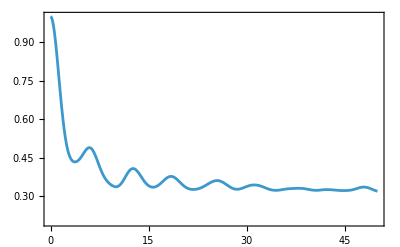

```mathematica
ListPlot[dataChaotic,
PlotRange->{{0,50},{0.2,1}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,FontSize->24,FontFamily->"Latin Modern Math"],
ImageSize->400
]
```

```mathematica
dataRegular=Import["~/Documents/chaos_meets_channels/ja_files/data/haar_avg_choi_purity/xxz/open/L_6_d_3_omega_0_Jz_1/epsilon_0.22_Jxy_0.73.csv","CSV"][[2;;]];
```

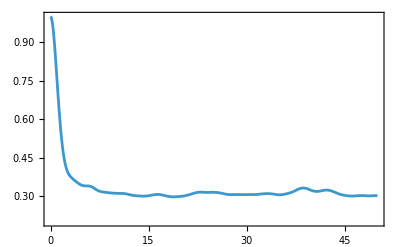

```mathematica
ListPlot[dataRegular,
PlotRange->{{0,50},{0.2,1}},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,FontSize->24,FontFamily->"Latin Modern Math"],
ImageSize->400
]
```